```mathematica
<<Local`SrednickiInit`
```

This notebook does the q[_] integrations first.

Problem 28.1

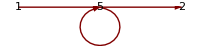
Review of Problem 14.5, the loop correction to the propagator for the φ^4 theory.  The O[λ] diagram:  -Graphics-The O[λ] self-energy that corresponds to (14.4) is: ⅈ Π[k^2]==-ⅈ (A k^2+B m^2)+λ IntegralOp[{l},-ⅈ Δ[l^2]]where: {A→-1+Z_φ,B→-1+Z_m}defined in the following Lagrangian.

```mathematica
PR[
"Review of Problem 14.5, the loop correction to the propagator for the φ^4 theory.  The O[λ] diagram:  ",
GraphPlot[{{1->5,k[1]},{5->5,q[1]},{5->2,k[1]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,0},2->{3,0},5->{1.5,0}} ,ImageSize->200],
"The O[λ] self-energy that corresponds to (14.4) is: ",
x144=ⅈ Π[k^2]==(ⅈ λ)^1/24(-ⅈ)(4!)IntegralOp[{l},(1/ⅈ)Δ[l^2]]-ⅈ(A k^2+B m^2),
"where: ",
defAB={A->Subscript[Z, φ]-1,B->Subscript[Z, m]-1},
"defined in the following Lagrangian."
]
```

```mathematica
PR[
"Following renormalization group procedure with(28.41):\n",
e2841=ℒ->-1/2 Subscript[Z, φ] guu[β,α]xPartialD[φ,α]xPartialD[φ,β]-1/2 Subscript[Z, m] m^2 φ^2-1/24 Subscript[Z, λ] λ (μ̃)^(ε/2)φ^4,
"\nand its bare field equation:",Yield,
b2841=ℒ->-1/2 guu[β,α]xPartialD[Subscript[φ, 0],α]xPartialD[Subscript[φ, 0],β]-1/2 Subscript[m, 0]^2 Subscript[φ, 0]^2-1/24 Subscript[λ, 0] Subscript[φ, 0]^4,
"\ndetermine the relationships:",Yield,
tmpr={Subscript[φ, 0]==√Subscript[Z, φ] φ,Subscript[m, 0]==√(Subscript[Z, m]/Subscript[Z, φ])m,Subscript[λ, 0]==(Subscript[Z, λ] λ (μ̃)^(ε/2))/Subscript[Z, φ]^2},
"\nWe use the expression for Z's, (28.9), (28.8), (28.7):",Yield,
e2809=Subscript[Z, λ]->1+HoldForm[Sum[(Subscript[c, n][α])/ε^n,{n,1,Inf}]],and ,
e2808=e2809/.{c->b,λ->m},and,
e2807=e2809/.{c->a,λ->φ},
"  where:  ",tmpα=α->(2 π^2 λ)/1,tmpαi=λ->α/(2 π^2);
"\nFrom the definition of λ_0:  ",tmp=tmpr[[3]],
"\nwe define: ",tmpα0=tmp/.λ->α/.Subscript[Z, α]->Subscript[Z, λ],and,x2814=G[α,ε]->Log[Last[tmpα0/.{α->1,μ̃->1}]]
]
```

Following renormalization group procedure with(28.41):
ℒ→-1/2 m^2 φ^2 Z_m-1/24 λ φ^4 (μ̃)^(ε/2) Z_λ-1/2 Z_φ g_βα^βα xPartialD[φ,α] xPartialD[φ,β]
and its bare field equation:
→ ℒ→-1/2 m_0^2 φ_0^2-1/24 λ_0 φ_0^4-1/2 g_βα^βα xPartialD[φ_0,α] xPartialD[φ_0,β]
determine the relationships:
→ {φ_0==φ √Z_φ,m_0==m √(Z_m/Z_φ),λ_0==(λ (μ̃)^(ε/2) Z_λ)/Z_φ^2}
We use the expression for Z's, (28.9), (28.8), (28.7):
→ Z_λ→1+∑_(n=1)^Inf c_n[α]/ε^n and Z_m→1+∑_(n=1)^Inf b_n[α]/ε^n and Z_φ→1+∑_(n=1)^Inf a_n[α]/ε^n  where:  α→2 π^2 λ
From the definition of λ_0:  λ_0==(λ (μ̃)^(ε/2) Z_λ)/Z_φ^2
we define: α_0==(α (μ̃)^(ε/2) Z_λ)/Z_φ^2 and G[α,ε]→Log[Z_λ/Z_φ^2]

```mathematica
PR["From (28.7) and (28.9):",Yield,
e2807," and ",e2809,", G can be expressed: ",Yield,
tmp=x2814/.e2807/.e2809,"Expanding this expression and ASSUMING that the a_n,c_n's are of O[α^n].  Here (iε->1/ε).:",Yield,
tmp=tmp/.ε->1/iε//ReleaseHold//PowerExpand;Yield;
n=1;
tmp=Series[tmp,{iε,0,n}]//Normal//ExpandAll;Yield;
tmp=tmp/.Subscript[_, _+Inf][_]->small/.small->0,
"We have expanded this series to ",O[α]^n,"  and expanding Log to 2nd order:",Yield,
tmp=tmp/.Log[1+f_]->f-f^2/2;
x2815=Collect[tmp,iε,Simplify],Yield;
coef2815=CoefficientList[x2815[[2]],iε];
]
```

From (28.7) and (28.9):
→ Z_φ→1+∑_(n=1)^Inf a_n[α]/ε^n and Z_λ→1+∑_(n=1)^Inf c_n[α]/ε^n, G can be expressed: 
→ G[α,ε]→Log[(1+∑_(n=1)^Inf c_n[α]/ε^n)/((1+∑_(n=1)^Inf a_n[α]/ε^n)^2)]Expanding this expression and ASSUMING that the a_n,c_n's are of O[α^n].  Here (iε->1/ε).:
→ G[α,1/iε]→-2 Log[1+iε a_1[α]+iε^2 a_2[α]]+Log[1+iε c_1[α]+iε^2 c_2[α]]We have expanded this series to O[α]^1  and expanding Log to 2nd order:
→ G[α,1/iε]→iε (-2 a_1[α]+c_1[α])+iε^2 (a_1[α]^2-2 a_2[α]-1/2 c_1[α]^2+c_2[α])+iε^3 (2 a_1[α] a_2[α]-c_1[α] c_2[α])+iε^4 (a_2[α]^2-1/2 c_2[α]^2)Null

```mathematica
PR["Differentiating the Log of ",tmpα0," wrt Log[μ] and requiring Dt[α_0,Log[μ]]->0 ",Yield,
tmp=tmpα0/.(Map[Exp[#]&,x2814]//Reverse);Yield;
tmp=Map[Log[#]&,tmp]//PowerExpand,Yield,
tmp=tmp/.μ̃->oμ;
tmp=Map[Dt[#,Log[μ],Constants->{ε,Subscript[α, 0]}]&,tmp];Yield;
tmp=tmp/.HoldPattern[Dt[a_,b_,c_]]->Dt[a,b];Yield;
tmp=tmp/.{Dt[a_,Log[μ]]:>a Dt[Log[a],Log[μ]],Dt[Log[oμ],Log[μ]]->1};Imply;
tmp=Collect[Map[α #&,tmp]//Expand,Dt[α,_]],
"Using the same arguement associated with (28.20):",Yield,
tmp=Solve[Apply[Equal,tmp],Dt[α,Log[μ]]][[1,1]],
"Approximating the 1/(1+f) factor:",Yield,
tmpdαdLμ=tmp=tmp/.(1/(1+f_)->Series[1/(1+f),{f,0,1}]//Normal),
"So the β function is:",Yield,
tmpβ0=tmp//Expand;
tmpb0=β[α]->tmpβ0[[2,2]]," where ",Yield,
tmp=Map[Dt[#,α,Constants->{iε}]&,x2815],Yield,
tmp[[2]]=Normal[Series[tmp[[2]],{iε,0,1}]];
sub=tmp/.iε->1/ε;
"Then to O[ε]^0:",Yield,
tmpβ=tmpb0/.sub
]
tmpβb=tmpβ0;tmpβb[[2,2]]=β[α];
tmpβb;
```

Differentiating the Log of α_0==(α (μ̃)^(ε/2) Z_λ)/Z_φ^2 wrt Log[μ] and requiring Dt[α_0,Log[μ]]->0 
→ Log[α_0]==G[α,ε]+Log[α]+1/2 ε Log[μ̃]
→ 0==(α ε)/2+Dt[α,Log[μ]] (1+α G^(1,0)[α,ε])Using the same arguement associated with (28.20):
→ Dt[α,Log[μ]]→-(α ε)/(2 (1+α G^(1,0)[α,ε]))Approximating the 1/(1+f) factor:
→ Dt[α,Log[μ]]→-1/2 α ε (1-α G^(1,0)[α,ε])So the β function is:
→ β[α]→1/2 α^2 ε G^(1,0)[α,ε] where 
→ G^(1,0)[α,1/iε]→iε (-2 (a_1)'[α]+(c_1)'[α])+iε^2 (2 a_1[α] (a_1)'[α]-2 (a_2)'[α]-c_1[α] (c_1)'[α]+(c_2)'[α])+iε^3 (2 a_2[α] (a_1)'[α]+2 a_1[α] (a_2)'[α]-c_2[α] (c_1)'[α]-c_1[α] (c_2)'[α])+iε^4 (2 a_2[α] (a_2)'[α]-c_2[α] (c_2)'[α])
→ Then to O[ε]^0:
→ β[α]→1/2 α^2 (-2 (a_1)'[α]+(c_1)'[α])

```mathematica
<<14.save;
<<16.save;
PR[
"We have an expressions for A,B from Problem 14.5 using dimensional regulation.",
subABdim,
tmpB=B/.subABdim,and,
"with minimal subtraction (MS): ",
tmpB[[2]]=Coefficient[tmpB[[2]],(1/ε)]/ε;Yield;
subABdim[[1]]=B->tmpB,Yield,
tmp=tmpφ4C[[1]]//Expand;Yield;
tmp[[2]]=Coefficient[tmp[[2]],1/ε]/ε;Yield;
"A,B,C is: ",
tmpABC={subABdim,tmp}//Flatten//Sort
]
```

We have an expressions for A,B from Problem 14.5 using dimensional regulation.{B→-λ/(16 π^2 ε)+(-λ+γ λ)/(32 π^2),A→0}-λ/(16 π^2 ε)+(-λ+γ λ)/(32 π^2) and with minimal subtraction (MS): B→-λ/(16 π^2 ε)
→ A,B,C is: {A→0,B→-λ/(16 π^2 ε),C→-λ/(8 π^2 ε)}

```mathematica
PR["From: ",tmpABC,and,
subA=Subscript[Z, φ]->A+1,and,subB=Subscript[Z, m]->B+1,and,subC=Subscript[Z, λ]->1+C,and,e2807,and,e2808,and,e2809,Yield,
Subscript[a, n][α]->0,and,tmp=Map[#-1&,e2808/.subB],imply,
tmp=tmp/.tmpABC//Reverse,Yield,
tmp=tmp/.Inf->1//ReleaseHold,yield,
tmpb=Map[# ε&,tmp],
"\nFor c_n: ",
tmp=Map[#-1&,e2809]/.subC/.tmpABC/.Inf->1//ReleaseHold,yield,
tmpc=Map[# ε&,tmp]//Reverse,
"\nIf we define: ",subα=λ->α(8 π^2),Yield,
sub={Subscript[a, 1][α]->0,tmpb,tmpc}/.subα;Yield;
sub=D[sub,α];Yield;
"The β function becomes: ",
tmpβ1=tmpβ/.sub
]
```

From: {A→0,B→-λ/(16 π^2 ε),C→-λ/(8 π^2 ε)} and Z_φ→1+A and Z_m→1+B and Z_λ→1+C and Z_φ→1+∑_(n=1)^Inf a_n[α]/ε^n and Z_m→1+∑_(n=1)^Inf b_n[α]/ε^n and Z_λ→1+∑_(n=1)^Inf c_n[α]/ε^n
→ a_1[α]→0 and B→∑_(n=1)^Inf b_n[α]/ε^n ⇒ ∑_(n=1)^Inf b_n[α]/ε^n→-λ/(16 π^2 ε)
→ b_1[α]/ε→-λ/(16 π^2 ε) ⟶ b_1[α]→-λ/(16 π^2)
For c_n: -λ/(8 π^2 ε)→c_1[α]/ε ⟶ c_1[α]→-λ/(8 π^2)
If we define: λ→8 π^2 α
→ The β function becomes: β[α]→-α^2/2

```mathematica
PR["Expression for bare mass, m_0 ",
tmp=tmpr⟦2⟧,"Take Log and comparing the two definitions of M[α,ε], (28.23), to O[α]: ",Yield,
tmpr2l=tmp=(Log[#1]&)/@tmp/.Log[a_ b_]->Log[a]+Log[b];defM={M[α,ε]->tmp⟦2,2⟧,M[α,ε]->HoldForm[∑_(n=1)^Inf (Subscript[M, n][α])/ε^n]},
"\nThe left equation: ",Yield;
tmp=PowerExpand[defM⟦1⟧];Yield;
tmp=tmp/.subB/.subA/.tmpABC/.subα;Yield;
tmp⟦2⟧=Series[tmp⟦2⟧,{α,0,1}];
tmp,
"The right equation to O[1/ε]: ",
tmpm=ReleaseHold[defM⟦2⟧/.Inf->1],Imply,tmpm1=Reverse[(#1 ε&)/@Normal[tmp⟦2⟧->tmpm⟦2⟧]],Yield;"\nThe anomalous dimension of m.  ",
"From: ",tmpr2l,and,defM[[1]],Yield,
tmp=tmpr2l/.Reverse[defM⟦1⟧],
"The derivative wrt Log[μ] where m_0 is constant.",Yield,
tmp=(Dt[#1,Log[μ],Constants->{ε,Subscript[m, 0]}]&)/@tmp;Yield;
tmp=tmp/.Dt->xDt/.xDt[a_,b_,c_]:>Dt[a,b];
tmp=tmp/.tmpdαdLμ/.{
Dt[M[α,ε],α]->-α/2,
Dt[M[α,ε],α,Constants->{ε,Subscript[m, 0]}]->D[tmpm1[[2]],α]
},
"Yield the anomalous dimension of the mass, γ_m[α]≡  ",yield,
tmp=tmp/.Solve[Apply[Equal,tmpb0],Dt[G[α,ε],α,Constants->{ε}]][[1]]//Expand;
tmp=tmp/.tmpβ1;
tmp=Map[-(#-tmp[[2,3]])&,tmp]/.ε->0
]
```

Expression for bare mass, m_0 m_0==m √(Z_m/Z_φ)Take Log and comparing the two definitions of M[α,ε], (28.23), to O[α]: 
→ {M[α,ε]→Log[√(Z_m/Z_φ)],M[α,ε]→∑_(n=1)^Inf M_n[α]/ε^n}
The left equation: M[α,ε]→-α/(4 ε)+O[α]^2The right equation to O[1/ε]: M[α,ε]→M_1[α]/ε
⇒ M_1[α]→-α/4
The anomalous dimension of m.  From: Log[m_0]==Log[m]+Log[√(Z_m/Z_φ)] and M[α,ε]→Log[√(Z_m/Z_φ)]
→ Log[m_0]==Log[m]+M[α,ε]The derivative wrt Log[μ] where m_0 is constant.
→ 0==Dt[m,Log[μ]]/m+1/8 α ε (1-α G^(1,0)[α,ε])Yield the anomalous dimension of the mass, γ_m[α]≡   ⟶ Dt[m,Log[μ]]/m==-α^2/8

```mathematica
PR[
"The anomalous dimension of φ:","Differentiating wrt Log[μ] of the Log of the propagator relationship (28.32): ",Yield,
tmp=Subscript[Δ̃, 0] [k^2] == Zφ  Δ̃ [k^2,f],Yield,
tmp=Map[Log[#]&,tmp]//PowerExpand,Yield,
tmp=Map[Dt[#,Log[μ],Constants->{k^2}]&,tmp];
tmp=tmp//DtRemove3,
New,"We investigate the first 3 terms of 28.07 ",
t2807=e2807/.{Subscript[Z, φ]->Zφ,Inf->2}//ReleaseHold,Yield,
t2807=Map[Log[#]&,t2807],Yield,
t2807[[2]]=Series[t2807[[2]]/.ε->1/εi,{εi,0,2}]//Normal;
t2807[[2]]=t2807[[2]]/.εi->1/ε;
t2807,Imply,
t2807=Map[Dt[#,Log[μ],Constants->{ε}]&,t2807];
t2807=t2807//DtRemove3,Yield,
t2807=t2807/.tmpβb//Simplify;Yield,
t2807[[2]]=Series[t2807[[2]]/.ε->1/εi,{εi,0,1}]//Normal;
t2807=t2807/.εi->1/ε,Yield,
"Since as ε->0 this relationship must vary smoothly with μ the terms each term of expansion of 1/ε must be zero.  Define the anomalous dimension of the field: ",
tmpγ=Subscript[γ, φ]->1/2 HoldForm[Dt[Log[Subscript[Z, φ]],Log[μ]]],
t2807[[1]]=2 tmpγ[[1]];
t2807[[2,2]]=0;
" and above we have: ",sub=Subscript[a, 1]->0,Yield,
t2807,Imply,t2807/.sub
]
```

Part::partw: Part 2 of (Dt → xDt)[Dt[Zφ, Log[μ], Constants → {ε}]/Zφ → Dt[α, Log[μ], Constants → {ε}] ((ε - _« 2 »[« 1 »]) SuperscriptBox[(a_1),  does not exist.

Part::partw: Part 2 of (Dt → xDt)[Dt[Zφ, Log[μ], Constants → {1/εi}]/Zφ → εi^2 Dt[α, Log[μ], Constants → {1/εi}] ((1/εi - _« 2 »[« 1 »]) SuperscriptBox[(a_1),  does not exist.

Part::partw: Part 2 of (Dt → xDt)[Dt[Zφ, Log[μ], Constants → {1/εi}]/Zφ → Dt[α, Log[μ], Constants → {1/εi}] (InterpretationBox[SuperscriptBox[(a_1),  does not exist.

General::stop: Further output of Part will be suppressed during this calculation.

Set::partw: Part 2 of (Dt → xDt)[Dt[Zφ, Log[μ], Constants → {ε}]/Zφ → Dt[α, Log[μ], Constants → {ε}] ((ε - _« 2 »[« 1 »]) SuperscriptBox[(a_1),  does not exist.

Set::partw: Part 2 of (Dt → xDt)[2 γ_φ] does not exist.

The anomalous dimension of φ:Differentiating wrt Log[μ] of the Log of the propagator relationship (28.32): 
→ (Δ̃)_0[k^2]==Zφ Δ̃[k^2,f]
→ Log[(Δ̃)_0[k^2]]==Log[Zφ]+Log[Δ̃[k^2,f]]
→ (Dt→xDt)[0==Dt[Zφ,Log[μ],Constants→{k^2}]/Zφ+(Dt[f,Log[μ],Constants→{k^2}] (Δ̃)^(0,1)[k^2,f])/(Δ̃[k^2,f])]NewWe investigate the first 3 terms of 28.07 Zφ→1+a_1[α]/ε+a_2[α]/ε^2
→ Log[Zφ]→Log[1+a_1[α]/ε+a_2[α]/ε^2]
→ Log[Zφ]→a_1[α]/ε+(-1/2 a_1[α]^2+a_2[α])/ε^2
⇒ (Dt→xDt)[Dt[Zφ,Log[μ],Constants→{ε}]/Zφ→(Dt[α,Log[μ],Constants→{ε}] (a_1)'[α])/ε+1/ε^2(-Dt[α,Log[μ],Constants→{ε}] a_1[α] (a_1)'[α]+Dt[α,Log[μ],Constants→{ε}] (a_2)'[α])]
→ 
→ (Dt→xDt)[Dt[Zφ,Log[μ],Constants→{ε}]/Zφ→(Dt[α,Log[μ],Constants→{ε}] ((ε-a_1[α]) (a_1)'[α]+(a_2)'[α]))/ε^2]
→ Since as ε->0 this relationship must vary smoothly with μ the terms each term of expansion of 1/ε must be zero.  Define the anomalous dimension of the field: γ_φ→1/2 Dt[Log[Z_φ],Log[μ]] and above we have: a_1→0
→ (Dt→xDt)[2 γ_φ]
⇒ (Dt→xDt)[2 γ_φ]

The following has no direct relevance to problem 28.1

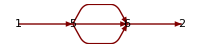
There are two corrections to the propagator to O[λ^2].  The single O[λ] and the double O[λ^2] loop corrections to propagator of ℒ_1⟶ φ^4:

The one-loop O[λ] contribution diagram: -Graphics-The two-loop O[λ^2] contribution diagram: -Graphics-We saw in Problem 14.5 that the one-loop diagram are exactly canceled by counter terms and does not contribute to the propagator correction so can be ignored.

```mathematica
PR[
"There are two corrections to the propagator to O[λ^2].  The single O[λ] and the double O[λ^2] loop corrections to propagator of ℒ_1⟶ φ^4:\n\nThe one-loop O[λ] contribution diagram: ",
GraphPlot[{{1->5,k[1]},{5->5,q[1]},{5->2,k[2]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,0},2->{3,0},5->{1.5,0}},ImageSize->200],
"The two-loop O[λ^2] contribution diagram: ",
GraphPlot[{{1->5,k[1]},{5->6,q[1]},{5->6,q[2]},{5->6,q[3]},{6->2,k[2]}},VertexLabeling->True,DirectedEdges-> True,MultiedgeStyle->.5,VertexCoordinateRules->{1->{0,0},2->{3,0},5->{1,0},6->{2,0}},ImageSize->200 ],
"We saw in Problem 14.5 that the one-loop diagram are exactly canceled by counter terms and does not contribute to the propagator correction so can be ignored."
]
```

```mathematica
PR["Attempt to compute two-loop contribution to propagator from ",
"(14.04) to O[λ^2]",Yield,
e1404=Π[k_]->1/2(I λ)^2(-I)^2 IntegralOp[{{q[1]},{q[2]},{q[3]}},1/(2 π)^d Δ̃[q[1]]Δ̃[q[2]]Δ̃[q[3]]DiracDelta[k-q[1]-q[2]-q[3]]]-(A k^2+B m^2),"\n",
e1403=Δ̃[q_]->1/(q^2+m^2-I ϵ);Yield,
t1404=e1404/.e1403,
"Transform using Feynmann parameterize integral.",Yield,
sub=1/(A1_ A2_ A3_)-> IntegralOp[{{F[3]}},(x[1] A1+x[2] A2+x[3] A3)^-3];
sub=sub/.e1410;
tmp=t1404/.sub,

"First do q[_] integrations.  Remove ϵ for notational ease.",Yield,
tmp=tmp//.subIntInt2IntNoExpand;
tmp=tmp//IntegralOpMoveNVarOutAll;
tmpI=Extract[tmp,Position[tmp,IntegralOp[__]]][[1]];
tmpI=tmpI/.ϵ->0 (*remove ϵ for notational ease *)
]
```

Attempt to compute two-loop contribution to propagator from (14.04) to O[λ^2]
→ Π[k_]→-A k^2-B m^2+1/2 λ^2 IntegralOp[{{q_1^1},{q_2^2},{q_3^3}},(2 π)^-d DiracDelta[k-q_1^1-q_2^2-q_3^3] Δ̃[q_1^1] Δ̃[q_2^2] Δ̃[q_3^3]]

→ Π[k_]→-A k^2-B m^2+1/2 λ^2 IntegralOp[{{q_1^1},{q_2^2},{q_3^3}},((2 π)^-d DiracDelta[k-q_1^1-q_2^2-q_3^3])/((m^2-ⅈ ϵ+(q_1^1)^2) (m^2-ⅈ ϵ+(q_2^2)^2) (m^2-ⅈ ϵ+(q_3^3)^2))]Transform using Feynmann parameterize integral.
→ Π[k_]→-A k^2-B m^2+1/2 λ^2 IntegralOp[{{q_1^1},{q_2^2},{q_3^3}},(2 π)^-d DiracDelta[k-q_1^1-q_2^2-q_3^3] IntegralOp[{{x_1^1,0,1},{x_2^2,0,1},{x_3^3,0,1}},(2 DiracDelta[-1+x_1^1+x_2^2+x_3^3])/(((m^2-ⅈ ϵ+(q_1^1)^2) x_1^1+(m^2-ⅈ ϵ+(q_2^2)^2) x_2^2+(m^2-ⅈ ϵ+(q_3^3)^2) x_3^3)^3)]]First do q[_] integrations.  Remove ϵ for notational ease.
→ IntegralOp[{{q_1^1},{q_2^2},{q_3^3},{x_1^1,0,1},{x_2^2,0,1},{x_3^3,0,1}},(DiracDelta[k-q_1^1-q_2^2-q_3^3] DiracDelta[-1+x_1^1+x_2^2+x_3^3])/(((m^2+(q_1^1)^2) x_1^1+(m^2+(q_2^2)^2) x_2^2+(m^2+(q_3^3)^2) x_3^3)^3)]

```mathematica
PR[
"The q[3] integral ",Yield,
tmpI1=evalDeltaIntOver[tmpI,q[3]],
"The q[2] integral: ",Yield,
quadratic=tmpId=tmpI1[[2]]//Denominator;
If[Head[tmpId]===Power,quadratic=tmpId[[1]]];
tlist=CompleteSquare[quadratic,q[2]];Yield;
tmp=tlist[[1]];Yield;
If[Head[tmpId]===Power,tmpId[[1]]=tmp,tmpId=tmp];Yield;
tmpI1[[2]]=tlist[[3,2]]Numerator[tmpI1[[2]]]/tmpId;Yield;
tmpI1=tmpI1/.{q[2]->h,d[h]->1};Yield;
tlist[[1]]=tmpI1;
tlist
]
```

The q[3] integral 
→ IntegralOp[{{q_1^1},{q_2^2},{x_1^1,0,1},{x_2^2,0,1},{x_3^3,0,1}},DiracDelta[-1+x_1^1+x_2^2+x_3^3]/(((m^2+(q_1^1)^2) x_1^1+(m^2+(q_2^2)^2) x_2^2+(m^2+(k-q_1^1-q_2^2)^2) x_3^3)^3)]The q[2] integral: 
→ {IntegralOp[{{q_1^1},{h},{x_1^1,0,1},{x_2^2,0,1},{x_3^3,0,1}},DiracDelta[-1+x_1^1+x_2^2+x_3^3]/((D+h^2)^3 √(x_2^2+x_3^3))],D→1/(x_2^2+x_3^3)(m^2 (x_2^2)^2+(k^2+2 m^2-2 k.q_1^1+(q_1^1)^2) x_2^2 x_3^3+m^2 (x_3^3)^2+(m^2+(q_1^1)^2) x_1^1 (x_2^2+x_3^3)),d[q_2^2]→d[h]/(√(x_2^2+x_3^3)),h→(q_2^2 x_2^2-k x_3^3+q_1^1 x_3^3+q_2^2 x_3^3)/(√(x_2^2+x_3^3)),q_2^2→(k x_3^3-q_1^1 x_3^3+h √(x_2^2+x_3^3))/(x_2^2+x_3^3)}

```mathematica
PR["Integrate over h",Yield,
tmpI2=tlist[[1]]/.IntegralOp[a_,b_]:>
SeparateIntVar1[{3,4,5,1,2},IntegralOp[a,b]],Yield,
tmp=tmpI2[[2,2,2,2]];
tmp=tmp/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b];Yield;
sub=e1427/.{q->h,d->4,b->3,a->0};
sub=Map[# 16 π^4&,sub]/.MoveIntOut;Yield;
tmp=tmp/.sub;
tmpI2[[2,2,2,2]]=tmp;
tmpI2,
"\nWhere:\n",
Rest[tlist]
]
tmpI2=tmpI2/.Rest[tlist];
```

Integrate over h
→ IntegralOp[{{x_1^1,0,1}},IntegralOp[{{x_2^2,0,1}},IntegralOp[{{x_3^3,0,1}},IntegralOp[{{q_1^1}},IntegralOp[{{h}},DiracDelta[-1+x_1^1+x_2^2+x_3^3]/((D+h^2)^3 √(x_2^2+x_3^3))]]]]]
→ IntegralOp[{{x_1^1,0,1}},IntegralOp[{{x_2^2,0,1}},IntegralOp[{{x_3^3,0,1}},IntegralOp[{{q_1^1}},(π^2 DiracDelta[-1+x_1^1+x_2^2+x_3^3])/(2 D √(x_2^2+x_3^3))]]]]
Where:
{D→1/(x_2^2+x_3^3)(m^2 (x_2^2)^2+(k^2+2 m^2-2 k.q_1^1+(q_1^1)^2) x_2^2 x_3^3+m^2 (x_3^3)^2+(m^2+(q_1^1)^2) x_1^1 (x_2^2+x_3^3)),d[q_2^2]→d[h]/(√(x_2^2+x_3^3)),h→(q_2^2 x_2^2-k x_3^3+q_1^1 x_3^3+q_2^2 x_3^3)/(√(x_2^2+x_3^3)),q_2^2→(k x_3^3-q_1^1 x_3^3+h √(x_2^2+x_3^3))/(x_2^2+x_3^3)}

```mathematica
PR[
"Integrate over q[1].",Yield,
tmpI3=tmpI2[[2,2,2]],Yield,
tmpI3=tmpI3/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b];Yield;
tmpI3a=Extract[tmpI3,tmpp=Position[tmpI3,IntegralOp[_,_]]][[1]];
tmpd=tmpI3a[[2]]//Denominator;
tmpn=tmpI3a[[2]]//Numerator;
"Complete square of q[1] in denominator.",Yield,
tlist1=CompleteSquare[tmpd,q[1]];
tmpI3a[[2]]=tlist1[[3,2]]tmpn/tlist1[[1]];Yield;
tmpI3a=tmpI3a/.{q[1]->h,d[h]->1};
tmpI3a=tmpI3a/.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b],
"Use dimensional regularization in 4-ε dimensions.",Yield,
sub=e1427/.{q->h,d->4-ε,b->1,a->0};
sub=Map[# 16 π^4&,sub]/.MoveIntOut/.a_^b_:>a^(b/.ε->0);Yield;
tmpI3a=tmpI3a/.sub;Yield;
tmpI3=ReplacePart[tmpI3,tmpp->tmpI3a];
tmpI3=ReplacePart[tmpI2,{2,2,2}->tmpI3];Yield;
tlist1[[1]]=tmpI3;
tlist1
]
```

Integrate over q[1].
→ IntegralOp[{{q_1^1}},(π^2 DiracDelta[-1+x_1^1+x_2^2+x_3^3] √(x_2^2+x_3^3))/(2 (m^2 (x_2^2)^2+(k^2+2 m^2-2 k.q_1^1+(q_1^1)^2) x_2^2 x_3^3+m^2 (x_3^3)^2+(m^2+(q_1^1)^2) x_1^1 (x_2^2+x_3^3)))]
→ Complete square of q[1] in denominator.
→ IntegralOp[{{h}},1/(D+h^2)]/(√(x_1^1 x_2^2+x_1^1 x_3^3+x_2^2 x_3^3))Use dimensional regularization in 4-ε dimensions.
→ {IntegralOp[{{x_1^1,0,1}},IntegralOp[{{x_2^2,0,1}},IntegralOp[{{x_3^3,0,1}},(D π^4 DiracDelta[-1+x_1^1+x_2^2+x_3^3] Gamma[1+1/2 (-4+ε)] √(x_2^2+x_3^3))/(2 √(x_1^1 x_2^2+x_1^1 x_3^3+x_2^2 x_3^3))]]],D→1/(x_2^2 x_3^3+x_1^1 (x_2^2+x_3^3))(x_2^2+x_3^3) (m^2 (x_1^1)^2 (x_2^2+x_3^3)+m^2 x_2^2 x_3^3 (x_2^2+x_3^3)+x_1^1 (m^2 (x_2^2)^2+(k^2+3 m^2) x_2^2 x_3^3+m^2 (x_3^3)^2)),d[q_1^1]→d[h]/(√(x_1^1 x_2^2+x_1^1 x_3^3+x_2^2 x_3^3)),h→(q_1^1 x_1^1 x_2^2+q_1^1 x_1^1 x_3^3-k x_2^2 x_3^3+q_1^1 x_2^2 x_3^3)/(√(x_1^1 x_2^2+x_1^1 x_3^3+x_2^2 x_3^3)),q_1^1→(k x_2^2 x_3^3+h √(x_1^1 x_2^2+x_1^1 x_3^3+x_2^2 x_3^3))/(x_1^1 x_2^2+x_1^1 x_3^3+x_2^2 x_3^3)}

```mathematica
PR[
"Integrate over x[3].",Yield,
tmp=tlist1[[1]]/.Rest[tlist1],Yield,
tmpp=Position[tmp,IntegralOp[_,_]];
tmpa=Extract[tmp,First[tmpp]];Yield;(*x[3] integral*)
tmpa=evalDeltaIntOver[tmpa,x[3]];Yield;
tmpa=tmpa//FullSimplify;Yield;
tmpI4=ReplacePart[tmp,First[tmpp]->tmpa],Yield,
"The integral expression may be easier to manipulate than the evaluated integral."
(*
tmpa=Extract[tmp,tmpp[[2]]];Yield;(*x[2] integral*)
tmpa=tmpa/.subxIntegrate,Yield,
tmpa=tmpa/.subIntegrate;Yield;
tmpa=tmpa//FullSimplify;Yield;
ReplacePart[tmp,tmpp[[2]]->tmpa];
tmp=tmp//.IntegralOp[a_,b_]:>IntegralOpMoveNVarOut[a,b];
*)

]
```

Integrate over x[3].
→ IntegralOp[{{x_1^1,0,1}},IntegralOp[{{x_2^2,0,1}},IntegralOp[{{x_3^3,0,1}},(π^4 DiracDelta[-1+x_1^1+x_2^2+x_3^3] Gamma[1+1/2 (-4+ε)] (x_2^2+x_3^3)^(3/2) (m^2 (x_1^1)^2 (x_2^2+x_3^3)+m^2 x_2^2 x_3^3 (x_2^2+x_3^3)+x_1^1 (m^2 (x_2^2)^2+(k^2+3 m^2) x_2^2 x_3^3+m^2 (x_3^3)^2)))/(2 √(x_1^1 x_2^2+x_1^1 x_3^3+x_2^2 x_3^3) (x_2^2 x_3^3+x_1^1 (x_2^2+x_3^3)))]]]
→ IntegralOp[{{x_1^1,0,1}},IntegralOp[{{x_2^2,0,1}},-(π^4 Gamma[-1+ε/2] (1-x_1^1)^(3/2) (m^2 (-1+x_2^2) x_2^2+(x_1^1)^2 (m^2+k^2 x_2^2)+x_1^1 (-1+x_2^2) (m^2+k^2 x_2^2)))/(2 (-(x_1^1)^2-x_1^1 (-1+x_2^2)+x_2^2-(x_2^2)^2)^(3/2))]]
→ The integral expression may be easier to manipulate than the evaluated integral.